# Creating Figures and Diagrams with Graphics Primitives

```mathematica
Disk[]
```

Disk[{0,0}]



```mathematica
Graphics[Disk[]]
```

```mathematica
Graphics[Disk[{0,-3},2]]
```

-Graphics-

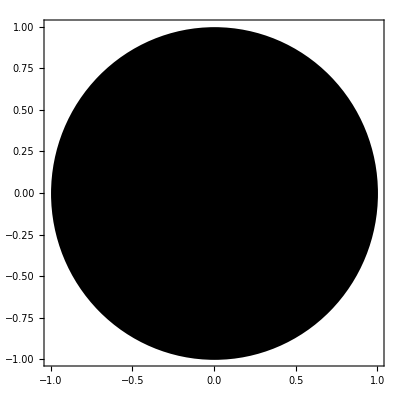

```mathematica
Graphics[Disk[],PlotRange->6,Frame->True]
```

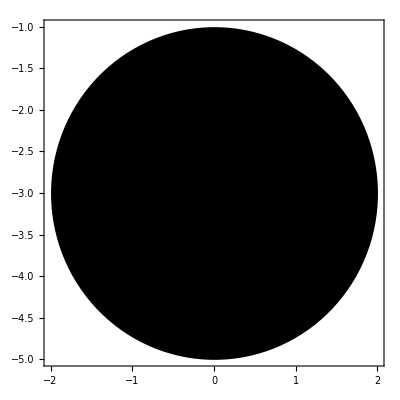

```mathematica
Graphics[Disk[{0,-3},2],PlotRange->6,Frame->True]
```

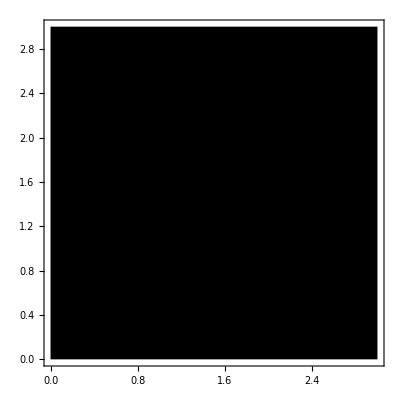

```mathematica
Graphics[Rectangle[{0,0},{3,3}],PlotRange->4,Frame->True]
```

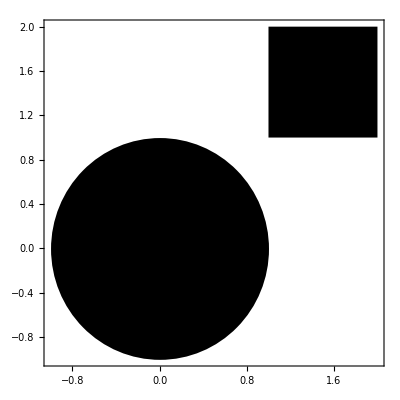

```mathematica
Graphics[{Disk[{0,0},1],Rectangle[{1,1},{2,2}]},PlotRange->2,Frame->True]
```

```mathematica
t=3;
d=1/2(-9.8)t^2+50;
```

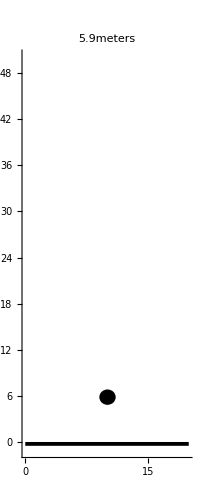

```mathematica
Graphics[{Disk[{10,d}],Rectangle[{0,-.5},{20,0}]},
PlotRange->{{0,20},{-1,50}},
Axes->{False,True},
PlotLabel->ToString[d]<>"meters"]
```

```mathematica
DynamicModule[{d,t},
Manipulate[Graphics[{Disk[{10,d[t]}],Rectangle[{0,-.5},{20,0}]},
PlotRange->{{0,20},{-1,50}},
PlotLabel->ToString[d[t]]<>"meters"],
{t,0,3.2},
Initialization:>(d[t_]:=1/2(-9.8)t^2+50)]]
```